# หาจุดกึ่งกลางของประเทศไทย

### โดย สมภพ ศรลัมพ์

```mathematica
THmap=EntityValue[LinguisticAssistant,"Polygon"][[1]]
```

GeoPosition[…]

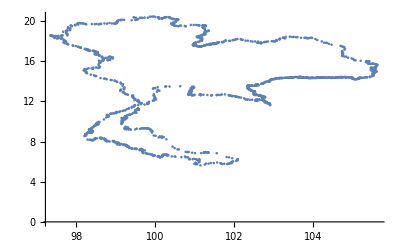

```mathematica
ListPlot[{#2,#1}&@@@(THmap[[1,1]])]
```

```mathematica
GeoListPlot[GeoPosition/@(THmap[[1,1]])]
```

-Graphics-

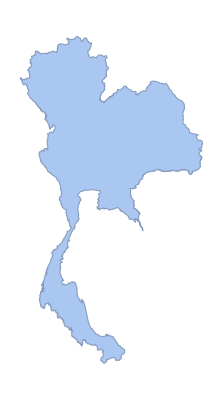

```mathematica
r=DiscretizeGraphics[Polygon[{#2,#1}&@@@(THmap[[1,1]])]]
```

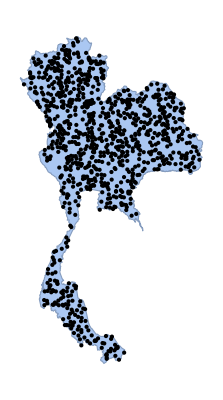

```mathematica
pnts=RandomPoint[r,1000];
Show[{r,Graphics/@Point/@pnts}]
```

```mathematica
DistFunc=SignedRegionDistance[r]
```

RegionDistanceFunction[…]

```mathematica
sols=Quiet@FindMinimum[DistFunc[{x,y}],{x,#[[1]]},{y,#[[2]]}]&/@pnts
```

{{-0.370482,{x→102.103,y→12.9238}},{-1.74993,{x→102.955,y→16.0757}},996,{-1.85305,{x→102.155,y→15.9033}},{-1.74462,{x→103.027,y→16.0939}}}
 |  |  |  |

```mathematica
nsols={#1,{x,y}/.#2}&@@@sols;
```

```mathematica
ans=TakeSmallestBy[nsols,First,1]//First
```

{-2.0197,{101.362,15.4575}}

```mathematica
GeoListPlot[{GeoPosition[ans[[2]]//RotateRight],LinguisticAssistant}]
```

-Graphics-

```mathematica
GeoGraphics[GeoMarker@GeoPosition[ans[[2,{2,1}]]],
GeoRange->Quantity[100,"Kilometers"]]
```

-Graphics-